## Preliminaries

```mathematica
(*for uniformity among figures*)
LabelSize=25;
FigureSize=650;
TickSize=16;
LetterSize=20;
Pad={{70,25},{70,10}};
letpos={.05,.93};
ylabpos={-0.1,0.5};

SetDirectory[NotebookDirectory[]];

(*directory to save figures in*)
imagedir="IMAGES/";

(*for plotting means with error bars*)
Needs["ErrorBarPlots`"]
```

## Simulation

```mathematica
DataMean=Import["/home/freek/Introgression/Example/08-05-2018-09-49-56/AlleleF_mean.csv","Data"];
DataVar=Import["/home/freek/Introgression/Example/08-05-2018-09-49-56/AlleleF_var.csv","Data"];
Needs["ErrorBarPlots`"]
```

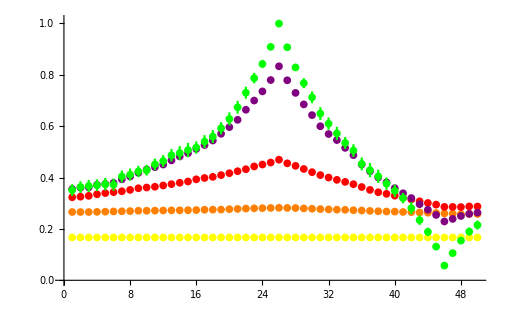

```mathematica
Show[
ErrorListPlot[Table[{DataMean[[1,2;;]][[i]],DataVar[[1,2;;]][[i]]},{i,1,50}],PlotRange->{0,1.01},PlotStyle->Yellow],
ErrorListPlot[Table[{DataMean[[5,2;;]][[i]],DataVar[[5,2;;]][[i]]},{i,1,50}],PlotRange->{0,1},PlotStyle->Orange],
ErrorListPlot[Table[{DataMean[[10,2;;]][[i]],DataVar[[10,2;;]][[i]]},{i,1,50}],PlotRange->{0,1},PlotStyle->Red],
ErrorListPlot[Table[{DataMean[[20,2;;]][[i]],DataVar[[20,2;;]][[i]]},{i,1,50}],PlotRange->{0,1},PlotStyle->Purple],
ErrorListPlot[Table[{DataMean[[50,2;;]][[i]],DataVar[[50,2;;]][[i]]},{i,1,50}],PlotRange->{0,1},PlotStyle->Green]
]
```

### KJB (2002) - 3 Locus model

Dynamics equations:

```mathematica
dpi=1/(1+s[i]p[i]+s[k]p[k])( s[i]p[i](1-p[i])+s[k]d[i,k])+p[i];
dpj=1/(1+s[i]p[i]+s[k]p[k])(s[i]d[i,j]+s[k]d[j,k])+p[j];
dpk=1/(1+s[i]p[i]+s[k]p[k])(s[k]p[k](1-p[k])+s[i]d[i,k])+p[k];
dij=1/(1+s[i]p[i]+s[k]p[k])(s[i](1-2p[i])d[i,j]+s[k]d[i,j,k])+d[i,j];
djk=1/(1+s[i]p[i]+s[k]p[k])(s[k](1-2p[k])d[j,k]+s[i]d[i,j,k])+d[j,k];
dik=1/(1+s[i]p[i]+s[k]p[k])(s[i]((1-2p[i])d[i,k])+s[k]((1-2p[k])d[i,k]))+d[i,k];
dijk=1/(1+s[i]p[i]+s[k]p[k])(s[i](p[i](1-p[i])d[j,k]+(1-2p[i])d[i,j,k])+s[k](p[k](1-p[k])d[i,j]+(1-2p[k])d[i,j,k]))+d[i,j,k];
```

Updating transmission:

```mathematica
ddpi=dpi;
ddpj=dpj;
ddpk=dpk;
ddij=(1-r[i,j])dij;
ddjk=(1-r[j,k])djk;
ddik=(1-r[i,k])dik;
ddijk=(1-r[i,j])(1-r[j,k])dijk;
```

Updating reference:

```mathematica
dddpi=ddpi//Simplify;
dddpj=ddpj//Simplify;
dddpk=ddpk//Simplify;
dddij=ddij-2(dpi-p[i])(dpj-p[j])//Simplify;
dddjk=ddjk-2(dpj-p[j])(dpk-p[k])//Simplify;
dddik=ddik-2(dpi-p[i])(dpk-p[k])//Simplify;
dddijk=ddijk-djk (dpi-p[i])-dik (dpj-p[j])-dij(dpk-p[k])+3(dpi-p[i]) (dpj-p[j]) (dpk-p[k])//Simplify;
```

```mathematica
Clear[Itterate3locus]
Itterate3locus[t_,p00_,si_,sk_,rij_,rjk_,rik_]:=Itterate3locus[t,p00,si,sk,rij,rjk,rik]=
Block[{p,d,i,r,j,k,s},
Itterate3locus[0,p00,si,sk,rij,rjk,rik]={p00,p00,p00,p00(1-p00),p00(1-p00),p00(1-p00),p00+2 p00^3-3 p00^2};
r[i,j]=rij;
r[j,k]=rjk;
r[i,k]=rik;
s[i]=si;
s[k]=sk;
p[i]=Itterate3locus[t-1,p00,si,sk,rij,rjk,rik][[1]];
p[j]=Itterate3locus[t-1,p00,si,sk,rij,rjk,rik][[2]];
p[k]=Itterate3locus[t-1,p00,si,sk,rij,rjk,rik][[3]];
d[i,j]=Itterate3locus[t-1,p00,si,sk,rij,rjk,rik][[4]];
d[j,k]=Itterate3locus[t-1,p00,si,sk,rij,rjk,rik][[5]];
d[i,k]=Itterate3locus[t-1,p00,si,sk,rij,rjk,rik][[6]];
d[i,j,k]=Itterate3locus[t-1,p00,si,sk,rij,rjk,rik][[7]];

{dddpi,
dddpj,
dddpk,
dddij,
dddjk,
dddik,
dddijk}
];
```

```mathematica
Itterate3locus[5,0.5,0.1,-0.1,0.1,0.1,0.1]
```

{0.522622,0.5,0.477378,0.146923,0.146923,0.146501,2.54069×10^-19}

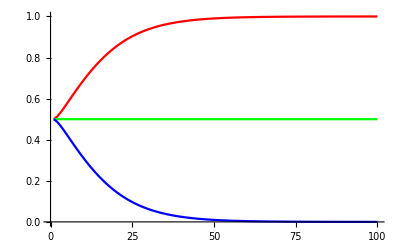

```mathematica
Show[
{ListLinePlot[Table[{t,Itterate3locus[t,0.5,0.1,-0.1,0.5,0.5,0.5][[1]]},{t,1,100}],PlotRange->{Automatic,{0,1}},PlotStyle->Red],
ListLinePlot[Table[{t,Itterate3locus[t,0.5,0.1,-0.1,0.5,0.5,0.5][[2]]},{t,1,100}],PlotRange->{Automatic,{0,1}},PlotStyle->Green],
ListLinePlot[Table[{t,Itterate3locus[t,0.5,0.1,-0.1,0.5,0.5,0.5][[3]]},{t,1,100}],PlotRange->{Automatic,{0,1}},PlotStyle->Blue]}]
```

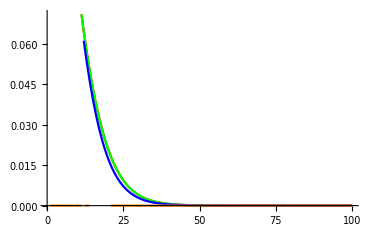

```mathematica
Show[
{ListLinePlot[Table[{t,Itterate3locus[t,0.5,0.1,-0.1,0.1,0.1,0.1][[4]]},{t,1,100}],PlotStyle->Red],
ListLinePlot[Table[{t,Itterate3locus[t,0.5,0.1,-0.1,0.1,0.1,0.1][[5]]},{t,1,100}],PlotStyle->Green],
ListLinePlot[Table[{t,Itterate3locus[t,0.5,0.1,-0.1,0.1,0.1,0.1][[6]]},{t,1,100}],PlotStyle->Blue],
ListLinePlot[Table[{t,Itterate3locus[t,0.5,0.1,-0.1,0.1,0.1,0.1][[7]]},{t,1,100}],PlotStyle->Orange]}]
```

```mathematica
Pars={pi0->4/24,pj0->4/24,pk0->4/24,si->0.2,sk->-0.05};
```

```mathematica
Qinf[accuracy_,c_,R0_,p0_,s_]:=c R0(1-p0)Sum[(1-c)^n/(1-p0+p0(1+s)^(n+1)),{n,0,accuracy}];
```

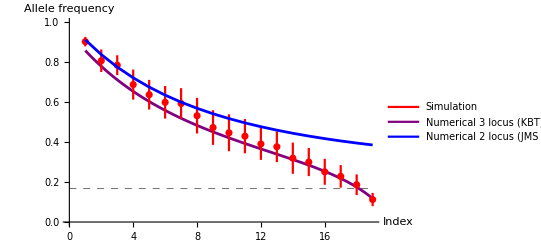

```mathematica
TotalDistance=20;
RecombRate=0.01;
Legended[Show[
ListLinePlot[Table[{nij,Itterate3locus[200,pi0/.Pars,si/.Pars,sk/.Pars,1-1/2 (1+(1-2 RecombRate)^nij),1-1/2 (1+(1-2 RecombRate)^(TotalDistance-nij)),1-1/2 (1+(1-2 RecombRate)^TotalDistance)][[2]]},{nij,1,TotalDistance-1,0.1}],PlotRange->{Automatic,{0,1}},PlotStyle->{Purple,Thickness[0.005]},AxesLabel->{"Index","Allele frequency"}],
ListLinePlot[
Table[{nij,pi0/.Pars},{nij,0,TotalDistance-1}],PlotStyle->{Thickness[0.001],Dashed,Black}],
ErrorListPlot[Table[{DataMean[[200,28;;46]][[i]],DataVar[[200,28;;46]][[i]]},{i,1,19}],PlotRange->{0,1},PlotStyle->Red],
ListLinePlot[Table[{n,1-Qinf[1000,1/2 (1-(1-2 RecombRate)^n),1,pi0/.Pars,si/.Pars]},{n,1,19}],PlotStyle->{Blue,Thickness[0.005]}]

],
LineLegend[{Red,Purple,Blue},{"Simulation","Numerical 3 locus (KBT)","Numerical 2 locus (JMS & JH)"}]
]
```

```mathematica
Export["/home/freek/Introgression/Example/Temp.pdf",%]
```

/home/freek/Introgression/Example/Temp.pdf

## 2 Locus model from KB to check with JMS

2 locus model (i,j) with two alleles segregating (1,0) and selection s_i and s_j and recombination rate r.

```mathematica
npi=si/(1+pi si)pi(1-pi)+pi;
npj=si/(1+pi si)Dij+pj;
nDij=(Dij+si/(1+pi si)(1-2pi)Dij)(1-rij)+(pi-npi)(pj-npj)//Simplify
```

(Dij (1+si-2 (-1+pi) pi si^2+rij (-1-si+(-1+pi) pi si^2)))/(1+pi si)^2

```mathematica
Clear[Itterate2locus]
Itterate2locus[t_,pi0_,si0_,sj0_,rij0_]:=Itterate2locus[t,pi0,si0,sj0,rij0]=Block[
{pi,pj,Dij,si,sj,rij},
Itterate2locus[0,pi0,si0,sj0,rij0]={pi0,pi0,pi0(1-pi0)};

si=si0;
sj=sj0;
rij=rij0;
pi=Itterate2locus[t-1,pi0,si0,sj0,rij0][[1]];
pj=Itterate2locus[t-1,pi0,si0,sj0,rij0][[2]];
Dij=Itterate2locus[t-1,pi0,si0,sj0,rij0][[3]];

{npi,npj,nDij}
]
```

```mathematica
Pars
```

{pi0→1/6,pj0→1/6,pk0→1/6,si→0.2,sk→-0.05}

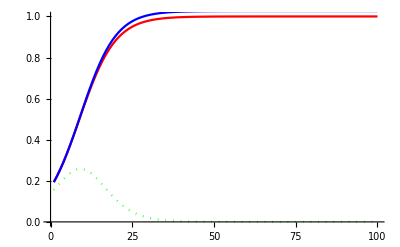

```mathematica
Show[
ListLinePlot[Table[{t,Itterate2locus[t,pi0/.Pars,0.2,0,0.01][[1]]},{t,1,100}],PlotStyle->{Red},PlotRange->{Automatic,{0,1}}],
ListLinePlot[Table[{t,Itterate2locus[t,pi0/.Pars,0.2,0,0.01][[2]]},{t,1,100}],PlotStyle->Blue,PlotRange->All],
ListLinePlot[Table[{t,Itterate2locus[t,pi0/.Pars,0.2,0,0.01][[3]]},{t,1,100}],PlotStyle->{Dotted,Green},PlotRange->All]
]
```

```mathematica
Pars
RecombRate
```

{pi0→1/6,pj0→1/6,pk0→1/6,si→0.2,sk→-0.05}

0.01

```mathematica
Table[{nij,Itterate2locus[200,pi0/.Pars,si/.Pars,0,1-1/2 (1+(1-2 RecombRate)^nij)][[2]]},{nij,1,20}]
```

{{1,1.02633},{2,0.937098},{3,0.861505},{4,0.796995},{5,0.741569},{6,0.693646},{7,0.651969},{8,0.615525},{9,0.583493},{10,0.555206},{11,0.530113},{12,0.507759},{13,0.487766},{14,0.469817},{15,0.453647},{16,0.439029},{17,0.425773},{18,0.413716},{19,0.402719},{20,0.392659}}

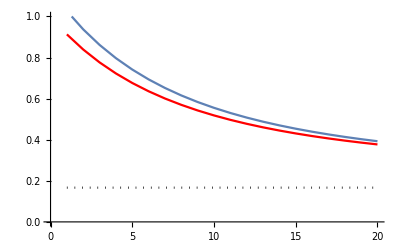

```mathematica
Show[
ListLinePlot[Table[{nij,Itterate2locus[100,pi0/.Pars,si/.Pars,0,1-1/2 (1+(1-2 RecombRate)^nij)][[2]]},{nij,1,20}],PlotRange->{Automatic,{0,1}}],
ListLinePlot[Table[{nij,1-Qinf[1000,1-1/2 (1+(1-2 RecombRate)^nij),1,pi0/.Pars,si/.Pars]},{nij,1,20}],PlotStyle->{Red},PlotRange->All],
ListLinePlot[Table[{nij,pi0/.Pars},{nij,1,20}],PlotStyle->{Black,Dotted}]
]
```

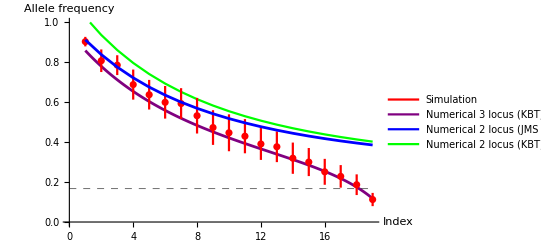

```mathematica
Legended[Show[
ListLinePlot[Table[{nij,Itterate3locus[200,pi0/.Pars,si/.Pars,sk/.Pars,1-1/2 (1+(1-2 RecombRate)^nij),1-1/2 (1+(1-2 RecombRate)^(TotalDistance-nij)),1-1/2 (1+(1-2 RecombRate)^TotalDistance)][[2]]},{nij,1,TotalDistance-1,0.1}],PlotRange->{Automatic,{0,1}},PlotStyle->{Purple,Thickness[0.005]},AxesLabel->{"Index","Allele frequency"}],
ListLinePlot[Table[{nij,Itterate2locus[200,pi0/.Pars,si/.Pars,0,1-1/2 (1+(1-2 RecombRate)^nij)][[2]]},{nij,1,19}],PlotRange->{Automatic,{0,1}},PlotStyle->Green],
ListLinePlot[
Table[{nij,pi0/.Pars},{nij,0,TotalDistance-1}],PlotStyle->{Thickness[0.001],Dashed,Black}],
ErrorListPlot[Table[{DataMean[[200,28;;46]][[i]],DataVar[[200,28;;46]][[i]]},{i,1,19}],PlotRange->{0,1},PlotStyle->Red],
ListLinePlot[Table[{n,1-Qinf[1000,1/2 (1-(1-2 RecombRate)^n),1,pi0/.Pars,si/.Pars]},{n,1,19}],PlotStyle->{Blue,Thickness[0.005]}]

],
LineLegend[{Red,Purple,Blue,Green},{"Simulation","Numerical 3 locus (KBT)","Numerical 2 locus (JMS & JH)","Numerical 2 locus (KBT)"}]
]
```

What is going wrong here, let’s find out

```mathematica
Solve[{pi Q==pi pj+Dij,pi(1-Q)==pi(1-pj)-Dij,(1-pi)R==(1-pi) pj-Dij,(1-pi)(1-R)==(1-pi)(1-pj)+Dij},{Dij,pj}]//Simplify
```

{{Dij→-(-1+pi) pi (Q-R),pj→pi (Q-R)+R}}

```mathematica
Qn=((1+pi s)Q+c(1-pi)(R-Q))/(1+pi s);
Rn=((1+pi s)R+c(1+s)pi(Q-R))/(1+pi s);
pin=pi(1+s)/(1+pi s);
```

```mathematica
Dijprime=(1-pin)pin(Qn-Rn)//FullSimplify
```

((-1+c) (-1+pi) pi (Q-R) (1+s))/(1+pi s)^2

```mathematica
((1-c) Dij (1+s))/(1+pi s)^2//Expand
```

Dij/(1+pi s)^2-(c Dij)/(1+pi s)^2+(Dij s)/(1+pi s)^2-(c Dij s)/(1+pi s)^2

```mathematica
(Dij (1-c+s-c s+(-1+pi) pi (-2+c) s^2))/(1+pi s)^2//Expand
```

Dij/(1+pi s)^2-(c Dij)/(1+pi s)^2+(Dij s)/(1+pi s)^2-(c Dij s)/(1+pi s)^2+(2 Dij pi s^2)/(1+pi s)^2-(c Dij pi s^2)/(1+pi s)^2-(2 Dij pi^2 s^2)/(1+pi s)^2+(c Dij pi^2 s^2)/(1+pi s)^2

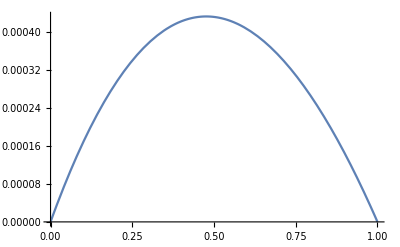

```mathematica
Plot[((2 Dij pi s^2)/(1+pi s)^2-(c Dij pi s^2)/(1+pi s)^2-(2 Dij pi^2 s^2)/(1+pi s)^2+(c Dij pi^2 s^2)/(1+pi s)^2)/.{s->0.1,Dij->0.1,c->0.1},{pi,0,1}]
```

```mathematica
pjprime=(((1-c) Dij (1+s))/(1+pi s)^2)/(1-pi)+Rn
```

((1-c) Dij (1+s))/((1-pi) (1+pi s)^2)+(c pi (Q-R) (1+s)+R (1+pi s))/(1+pi s)

The problem seems to be that there is first selection and then reproduction

## Numerical solution haploids

Assuming exponential growth of the invader and resident assumes that the populations remain small. When populations are larger, density dependence should be taken into account.

```mathematica
nInv[t]/nRes[t]/(nInv[t-1]/nRes[t-1])/.param//Simplify
```

ⅇ^(2.31254 t)/10

```mathematica
nInv[t-1]/(nInv[t-1]+nRes[t-1])/.t->1/.param//Simplify
```

1/11

```mathematica
param={rRes->Log[0.1],rInv->Log[1.01],kRes->10,kInv->1,Θ->1};
```

```mathematica
nRes[t_]:=kRes*Exp[(t)*rRes];
nInv[t_]:=kInv*Exp[(t)*rInv];
```

```mathematica
Clear[simulatefrac]
simulatefrac[t_,rRes_,rInv_,kRes_,kInv_,Θ_]:=simulatefrac[t,rRes,rInv,kRes,kInv,Θ]=
Block[{
fracRes=simulatefrac[t-1,rRes,rInv,kRes,kInv,Θ][[1]],
fracInv=simulatefrac[t-1,rRes,rInv,kRes,kInv,Θ][[2]]},

nRes[t-1]=kRes*Exp[(t-1)*rRes];
nInv[t-1]=kInv*Exp[(t-1)*rInv];
newfracRes=(1/2*fracRes+1/2*fracInv)*nInv[t-1]/(nInv[t-1]+nRes[t-1]Θ)+(fracRes)*(nRes[t-1]Θ)/(nInv[t-1]+nRes[t-1]Θ);(*This is the equation describing how the genomic background changes for an individual carrying A, depending on who it mates with.*)
newfracInv=(1/2*fracRes+1/2*fracInv)*nRes[t-1]/(nInv[t-1]Θ+nRes[t-1])+(fracInv)*(nInv[t-1]Θ)/(nInv[t-1]Θ+nRes[t-1]);
(*This is the equation describing how the genomic background changes for an individual carrying a, depending on who it mates with.*)
{newfracRes,newfracInv} 
]
simulatefrac[0,rRes/.param,rInv/.param,kRes/.param,kInv/.param,Θ/.param]={1,0};
```

```mathematica
Qinf[c_]:=c R0(1-p0)Sum[(1-c)^n/(1-p0+p0(1+s)^(n+1)),{n,0,100}];
```

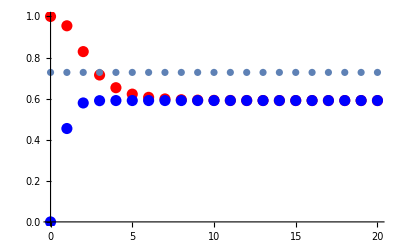

```mathematica
Show[
ListPlot[Table[{t,simulatefrac[t,rRes/.param,rInv/.param,kRes/.param,kInv/.param,Θ/.param][[1]]},{t,0,20}],PlotStyle->{PointSize[0.02],Red},PlotRange->{{0,20},{0,1}}],
ListPlot[Table[{t,simulatefrac[t,rRes/.param,rInv/.param,kRes/.param,kInv/.param,Θ/.param][[2]]},{t,0,20}],PlotStyle->{PointSize[0.02],Blue},PlotRange->{{0,20},{0,1}}],
ListPlot[Table[{t,Qinf[0.5]/.R0->1/.p0->1/11/.s->10.1-1},{t,0,20}]]

]
```

```mathematica
(kRes/(kRes+kInv))/.param//N
```

0.909091

```mathematica
Plot[(1-0.5)^t,{t,0,10},PlotRange->All]
```

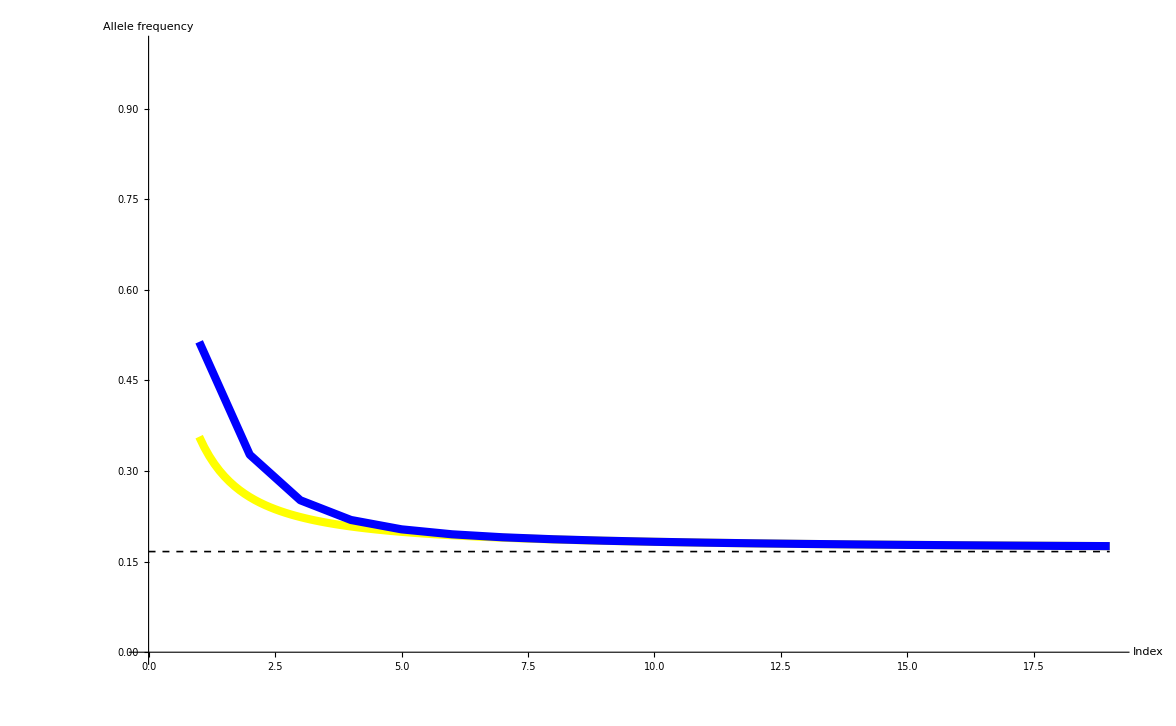

## Approximation to order a^2

```mathematica
api=p[i]+((1-p[i]) p[i] s[i]+d[i,k] s[k])/(1+p[i] s[i]+p[k] s[k]);
apj=p[j]+(d[i,j] s[i]+d[j,k] s[k])/(1+p[i] s[i]+p[k] s[k]);
apk=p[k]+(d[i,k] s[i]+(1-p[k]) p[k] s[k])/(1+p[i] s[i]+p[k] s[k]);
adij=(1-r[i,j])(d[i,j]);
adjk=(1-r[j,k])(d[j,k]);
adik=(1-r[i,k])(d[i,k]);
adijk=(1-r[i,j])(1-r[j,k])(d[i,j,k]);
```

```mathematica
Clear[itterateapprox]
itterateapprox[t_,p00_,si_,sk_,rij_,rjk_,rik_]:=itterateapprox[t,p00,si,sk,rij,rjk,rik]=
Block[{p,d,i,r,j,k,s},
r[i,j]=rij;
r[j,k]=rjk;
r[i,k]=rik;
s[i]=si;
s[k]=sk;
p[i]=itterateapprox[t-1,p00,si,sk,rij,rjk,rik][[1]];
p[j]=itterateapprox[t-1,p00,si,sk,rij,rjk,rik][[2]];
p[k]=itterateapprox[t-1,p00,si,sk,rij,rjk,rik][[3]];
d[i,j]=itterateapprox[t-1,p00,si,sk,rij,rjk,rik][[4]];
d[j,k]=itterateapprox[t-1,p00,si,sk,rij,rjk,rik][[5]];
d[i,k]=itterateapprox[t-1,p00,si,sk,rij,rjk,rik][[6]];
d[i,j,k]=itterateapprox[t-1,p00,si,sk,rij,rjk,rik][[7]];

{api,
apj,
apk,
adij,
adjk,
adik,
adijk}
];
itterateapprox[0,0.5,0.1,-0.1,0.1,0.1,0.1]={p00,p00,p00,p00(1-p00),p00(1-p00),p00(1-p00),p00+2 p00^3-3 p00^2}/.p00->0.5;
```

```mathematica
itterateapprox[5,0.5,0.1,-0.1,0.1,0.1,0.1]
```

{0.522561,0.5,0.477439,0.147623,0.147623,0.147623,0.}

```mathematica
Clear[endpointapprox]
endpointapprox[tend_,p00_, si0_,sk0_,rij0_,rjk0_,rik0_]:=
Block[{},
itterateapprox[0,p00,si0,sk0,rij0,rjk0,rik0]={p00,p00,p00,p00(1-p00),p00(1-p00),p00(1-p00),p00+2 p00^3-3 p00^2};
itterateapprox[tend,p00,si0,sk0,rij0,rjk0,rik0]
]
```

```mathematica
1-1/2 (1+(1-2 r)^nij)/.r->0.1/.nij->1
```

0.1

```mathematica
Pars={pi0->0.1,pj0->0.1,pk0->0.1,si->0.2,sk->-0.05,rij->0.3,rjk->0.3,rik->0.5,Dij0->0.25,Djk0->0.25}
```

{pi0→0.1,pj0→0.1,pk0→0.1,si→0.2,sk→-0.05,rij→0.3,rjk→0.3,rik→0.5,Dij0→0.25,Djk0→0.25}

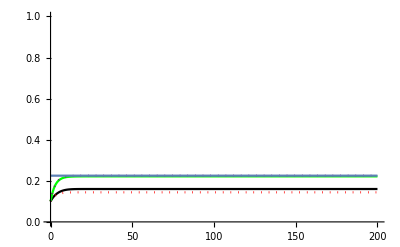

```mathematica
Show[{
ListLinePlot[Table[{t,endpoint[t,pi0/.Pars,si/.Pars,sk/.Pars,rij/.Pars,rjk/.Pars,rik/.Pars][[2]]},{t,0,200}],PlotStyle->{Black},PlotRange->{Automatic,{0,1}}],
ListLinePlot[Table[{t,endpointapprox[t,pi0/.Pars,si/.Pars,sk/.Pars,rij/.Pars,rjk/.Pars,rik/.Pars][[2]]},{t,0,200}],PlotStyle->{Red,Dotted},PlotRange->All],
ListLinePlot[Table[{t,pj0+Sum[(Dij0 (1-rij)^(-1+i) si+Djk0 (1-rjk)^(-1+i) sk)/(1+si/(1+ⅇ^(si-i si) (-1+1/pi0))+sk/(1+ⅇ^(sk-i sk) (-1+1/pk0))),{i,1,t}]/.Pars},{t,0,200}],PlotStyle->{Green},PlotRange->All],
ListLinePlot[Table[{t,pj0+Sum[Dij0 (1-rij)^(-1+i) si+Djk0 (1-rjk)^(-1+i) sk,{i,1,t}]/.Pars},{t,0,200}],PlotStyle->{Purple,Dotted},PlotRange->All],
ListLinePlot[Table[{t,pj0+(Dij0 rjk si+Djk0 rij sk)/(rij rjk)/.Pars},{t,0,200}],PlotRange->All]}
]
```

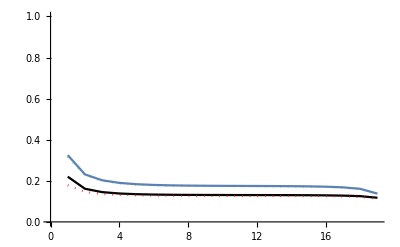

```mathematica
Show[
ListLinePlot[Table[{nij,endpoint[200,pi0/.Pars,si/.Pars,sk/.Pars,1-1/2 (1+(1-2 0.2)^nij),1-1/2 (1+(1-2 0.2)^(20-nij)),1-1/2 (1+(1-2 0.2)^20)][[2]]},{nij,1,19}],PlotStyle->{Black},PlotRange->{Automatic,{0,1}}],
ListLinePlot[Table[{nij,endpointapprox[200,pi0/.Pars,si/.Pars,sk/.Pars,1-1/2 (1+(1-2 0.2)^nij),1-1/2 (1+(1-2 0.2)^(20-nij)),1-1/2 (1+(1-2 0.2)^20)][[2]]},{nij,1,19}],PlotStyle->{Red,Dotted},PlotRange->All],
ListLinePlot[Table[{nij,pj0+Sum[(Dij0 (1-(1-1/2 (1+(1-2 0.2)^nij)))^(-1+i) si+Djk0 (1-(1-1/2 (1+(1-2 0.2)^(20-nij))))^(-1+i) sk)/(1+si/(1+ⅇ^(si-i si) (-1+1/pi0))+sk/(1+ⅇ^(sk-i sk) (-1+1/pk0))),{i,1,200}]/.Pars},{nij,1,19}],PlotStyle->{Green,Dotted},PlotRange->All],
ListLinePlot[Table[{nij,pj0+(Dij0 (1-1/2 (1+(1-2 0.2)^(20-nij))) si+Djk0 (1-1/2 (1+(1-2 0.2)^nij)) sk)/((1-1/2 (1+(1-2 0.2)^nij)) (1-1/2 (1+(1-2 0.2)^(20-nij))))/.Pars},{nij,1,19}],PlotRange->All]
]
```

```mathematica
Table[{nij,endpoint[200,pi0/.Pars,si/.Pars,sk/.Pars,1-1/2 (1+(1-2 0.2)^nij),1-1/2 (1+(1-2 0.2)^(20-nij)),1-1/2 (1+(1-2 0.2)^20)][[2]]},{nij,1,19}]
```

{{1,0.220095},{2,0.161307},{3,0.14496},{4,0.138182},{5,0.13484},{6,0.133042},{7,0.132027},{8,0.131434},{9,0.131077},{10,0.13085},{11,0.130689},{12,0.130548},{13,0.13039},{14,0.130166},{15,0.129805},{16,0.129169},{17,0.127952},{18,0.125291},{19,0.117433}}

0.935642

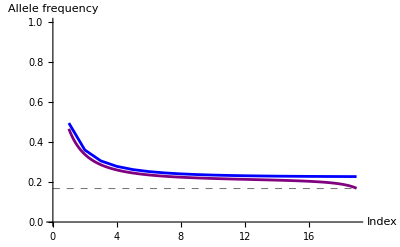

```mathematica
endpoint[200,pi0/.Pars,si/.Pars,sk/.Pars,0,0.5,0.5][[2]]
```